```mathematica
RSolve[{a[n,m]== a[n-1,m]+1+m-2*((1+m)/2)^(n+1),a[0,m]==0},a[n,m],n]
```

{{a[n,m]→(2^-n (1+m) (2^n+2^n m-(1+m)^n-m (1+m)^n-2^n n+2^n m n))/(-1+m)}}

```mathematica
a[n_,m_]:=(2^-n (1+m) (2^n+2^n m-(1+m)^n-m (1+m)^n-2^n n+2^n m n))/(-1+m)
```

```mathematica
FullSimplify[a[n,m]]
```

(2^-n (-(1+m)^(2+n)+2^n (1+m) (1+m+(-1+m) n)))/(-1+m)

```mathematica
a[1,m]
```

((1+m) (-1+3 m-m (1+m)))/(2 (-1+m))

```mathematica
FullSimplify[(1+m)^3/(1-m)]
```

-(1+m)^3/(-1+m)

```mathematica
Limit[a[n,m]/n,n->Infinity]
```

Limit[(2^-n (1+m) (2^n+2^n m-(1+m)^n-m (1+m)^n-2^n n+2^n m n))/((-1+m) n),n→∞]

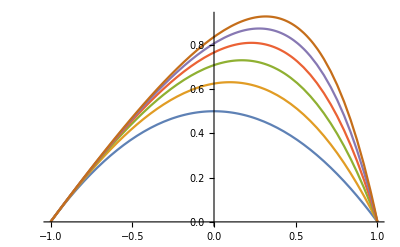

```mathematica
Plot[{a[1,m]/1,a[2,m]/2,a[3,m]/3,a[4,m]/4,a[5,m]/5,a[6,m]/6},{m,-1,1}]
```

```mathematica
FullSimplify[a[5,ms]]
```

-1/32 (-1+ms) (1+ms) (129+ms (72+ms (30+ms (8+ms))))

```mathematica
FullSimplify[(a[n,s]*(1-s)/(1+s)-n(1-s))/(1+s)]
```

-1+2^-n (1+s)^n

```mathematica
a = FullSimplify[D[a[n,s],s]]
```

(2^-n ((1+s)^(1+n) (3+n-(1+n) s)+2^n (n (-1+s)^2+(-3+s) (1+s))))/(-1+s)^2

```mathematica
FullSimplify[Limit[a,s->1]]
```

-1/2 n (1+n)

```mathematica
s
```

s